```mathematica
(* Filename: Errors_vs_Time_By_w2_revA_SRCK2_avr_Al_DN
*)
(* Ver. 0 (28-Aug-2025) *)
(*
This file is a program code in Mathematica to get a plot about errors in Fig. 2.
*)
(*
Note that the following files should be excuted before this program:
a) Errors_By_w2_revA_SRCK2_avr_Al_DN,
    b) Time_By_w2_revA_SRCK2_avr_Al_DN.
*)
```

```mathematica
fdim=2;
```

```mathematica
difflistMomAndTimeAForAve=Table[{},{ii,1,fdim}];
tmpMini=Table[{},{ii,1,5}];
For[ii=1, ii≤fdim, ii++,
tmpMini[[1]]={Log[2,timeA80Ave],Log[2,errorMomA80Ave[[ii]]]};
tmpMini[[2]]={Log[2,timeA53Ave],Log[2,errorMomA53Ave[[ii]]]};
tmpMini[[3]]={Log[2,timeA38Ave],Log[2,errorMomA38Ave[[ii]]]};
tmpMini[[4]]={Log[2,timeA28Ave],Log[2,errorMomA28Ave[[ii]]]};
tmpMini[[5]]={Log[2,timeA19Ave],Log[2,errorMomA19Ave[[ii]]]};
difflistMomAndTimeAForAve[[ii]]=Table[tmpMini[[ii]],{ii,1,5}];
];
```

```mathematica
plotlistMomAndTimeAForAve=Table[{},{ii,1,fdim}];
For[ii=1, ii≤fdim, ii++,
plotlistMomAndTimeAForAve[[ii]]=ListPlot[difflistMomAndTimeAForAve[[ii]],PlotMarkers->{Graphics[{EdgeForm[{Thickness[0.1],Red}],Opacity[0],Disk[]}],Scaled[0.035]}];
];
```

numSubSetForData=8

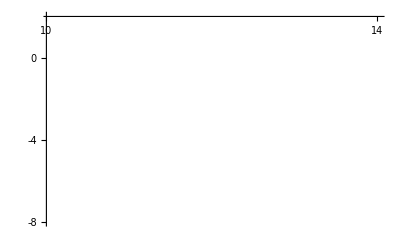

```mathematica
ll=0.03;
Print["numSubSetForData=",numSubSetForData];
ii=1;
Show[plotlistMomAndTimeAForAve[[ii]],PlotRange->{{10+0.05,14},{-8,2}},AxesOrigin->{10,2},Ticks->{Table[{1ii,ToString[1ii],ll},{ii,2,20}],Table[{-2ii,ToString[-2ii],ll},{ii,-2,8}]},BaseStyle->{14,FontFamily->"Helvetica"}]
```